# Actividad 2

## Wei Le Hu Tang

Calcular las ecuaciones de movimiento, el tiempo donde la restricción deja de existir así como las trayectorias, velocidades y aceleraciones para la trayectoria donde la restricción se anula y donde ésta continua. Pueden utilizar como apoyo el notebook de partícula deslizante.

Graficamos la restricción

```mathematica
res=Solve[4x^2+20y^2==45,y]
```

{{y→-(√(45-4 x^2))/(2 √5)},{y→(√(45-4 x^2))/(2 √5)}}

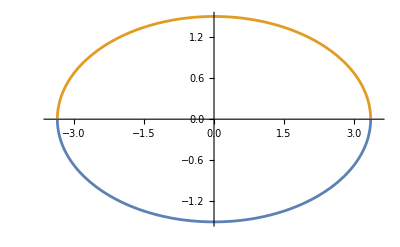

```mathematica
Plot[Evaluate[y/.res],{x,-3.5,3.5}]
```

Graficamos la región de interés

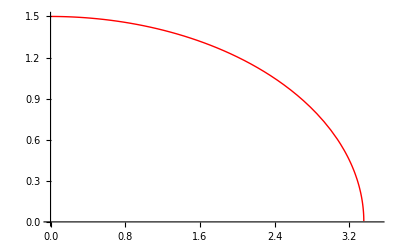

```mathematica
(*Gráfica de la resbaladilla*)
a=Plot[{Sqrt[(45-4*x^2)/20]},{x,0,3.5},PlotStyle->{Red,Thick}]
```

Obtenemos la segunda derivada temporal de la restricción




	(1)

Recordando que el Lagrangiano es la suma de energías potencial y cinética, donde
 por el teorema de Pitágoras, el cuadrado de la velocidad total puede ser visto como la suma de los cuadrados de sus componentes
 lo cual es negativo por la conservación de la energía y porque la gravedad “jala hacia abajo” a la masa
Considerando además la restricción, ésto es:

Se resuelven las derivadas parciales para obtener las ecuaciones de Euler-Lagrange




		(2*)

		(2)




		(3*)


	(3)

Usando (1), (2) y (3)

		(4)



Usando (2*) 




Regresando a (4)
	



Usando (3*) 





Se define la gravedad como , y el punto inicial

```mathematica
g=9.807;
x0=0.01;
```

Obtenemos el momento en el que la partícula llega al suelo que es cuando

```mathematica
{sol1,pt1}=Reap@NDSolve[{x''[t]==((5g*y[t]-x'[t]^2-5y'[t]^2)*x[t])/(x[t]^2+25y[t]^2),y''[t]==(5g*y[t]-x'[t]^2-5(y'[t]^2))*5y[t]/(x[t]^2+25y[t]^2)-g,x'[0]==0,y'[0]==0,x[0]==x0,y[0]==Sqrt[(45-4*x0^2)/20],WhenEvent[y[t]==0,Sow[{t,x[t]},1]]},{x,y},{t,0,6}];
pt1
```

{{{5.7701,3.3541}}}

La partícula llega al suelo al momento , a distancia horizontal 

Con esta información, se puede graficar numéricamente la trayectoria de la partícula

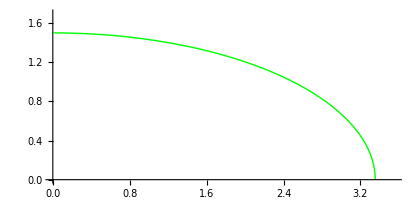

```mathematica
sol=NDSolve[{x''[t]==((5g*y[t]-x'[t]^2-5y'[t]^2)*x[t])/(x[t]^2+25y[t]^2),y''[t]==(5g*y[t]-x'[t]^2-5(y'[t]^2))*5y[t]/(x[t]^2+25y[t]^2)-g,x'[0]==0,y'[0]==0,x[0]==x0,y[0]==Sqrt[(45-4*x0^2)/20]},{x,y},{t,0,pt1[[1,1,1]]}];
(*Gráfica de la trayectoria*)
b=ParametricPlot[{x[t],y[t]}/.sol,{t,0,pt1[[1,1,1]]},PlotRange->{{0,pt1[[1,1,2]]+.2},{0,1.7}},PlotStyle->{Green,Thick}]
```

Calculamos el momento en que la partícula se despega de la restricción, que es cuando , pues la partícula deja de acelerarse horizontalmente, quedando en tiro parabólico y manteniendo velocidad constante. O bien, cuando  cuando verticalmente se alcanza la aceleración de la gravedad nos indica que el objeto se encuentra en caída libre, es decir, despegado de la restricción.

Más aun, matemáticamente, la restricción se anula cuando , entonces regresando a (2) y (3), se tiene que:

{{{5.57148,3.03216,2.19008×10^-12,-9.807,2.90474,0.749997}}}

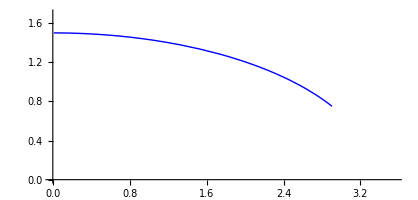

{{{5.57148,3.03216,1.1925×10^-14,-9.807,2.90474,0.749997}}}

-Graphics-

```mathematica
(*Utilizando la condición de la aceleración horizontal*)
{sol2,pt2}=Reap@NDSolve[{x''[t]==((5g*y[t]-x'[t]^2-5y'[t]^2)*x[t])/(x[t]^2+25y[t]^2),y''[t]==(5g*y[t]-x'[t]^2-5(y'[t]^2))*5y[t]/(x[t]^2+25y[t]^2)-g,x'[0]==0,y'[0]==0,x[0]==x0,y[0]==Sqrt[(45-4*x0^2)/20],WhenEvent[x''[t]==0,Sow[{t,x'[t],x''[t],y''[t],x[t],y[t]},1]]},{x,y},{t,0,t0}];
pt2
(*Gráfica del desplazamiento de la partícula sobre la restricción, antes de despegarse*)
c=ParametricPlot[{x[t],y[t]}/.sol,{t,0,pt2[[1,1,1]]},PlotRange->{{0,pt1[[1,1,2]]+.2},{0,1.7}},PlotStyle->{Blue,Thick}]

(*Utilizando la condición de la aceleración vertical*)
{sol2,pt2}=Reap@NDSolve[{x''[t]==((5g*y[t]-x'[t]^2-5y'[t]^2)*x[t])/(x[t]^2+25y[t]^2),y''[t]==(5g*y[t]-x'[t]^2-5(y'[t]^2))*5y[t]/(x[t]^2+25y[t]^2)-g,x'[0]==0,y'[0]==0,x[0]==x0,y[0]==Sqrt[(45-4*x0^2)/20],WhenEvent[y''[t]==-g,Sow[{t,x'[t],x''[t],y''[t],x[t],y[t]},1]]},{x,y},{t,0,t0}];
pt2
(*Gráfica del desplazamiento de la partícula sobre la restricción, antes de despegarse*)
c=ParametricPlot[{x[t],y[t]}/.sol,{t,0,pt2[[1,1,1]]},PlotRange->{{0,pt1[[1,1,2]]+.2},{0,1.7}},PlotStyle->{Blue,Thick}]
```

Nótese que en ambos casos, se obtuvieron prácticamente los mismos resultados, lo que nos dice que las dos condiciones sí son equivalentes, concluyendo entonces que la partícula se despega al momento , cuando  , que es básicamente 0,  y  , consiguiendo una velocidad horizontal constante de . Y el punto de separación en el plano es el 

A continuación se presenta la trayectoria de la partícula con respecto a la restricción

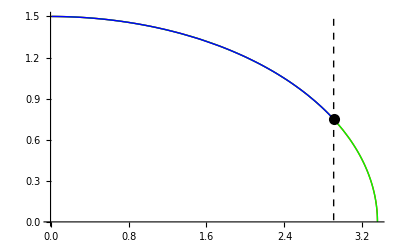

```mathematica
Show[a,b,c,PlotRange->All,Epilog->{{Black,PointSize[0.02],Point[{pt2[[1,1,5]],pt2[[1,1,6]]}]},{Black,Dashed,Line[{{pt2[[1,1,5]],-30},{pt2[[1,1,5]],30}}]}}]
```